Autocorrelations for Generalised Hybrid Monte Carlo

## Quadratic Operators with Fixed Length Trajectories

Based on the papeτ, “Cost of the Generalised Hybrid Monte Carlo Algorithm for Free Field Theory”, this notebook contains a Mathematica format for selected equations. The aim is to provide a dynamic method of working with the theory.

The paper provides the Laplace Transform of the autocorrelations which will be denoted by F[...] where β is the Laplace transformed time, t

Unless explicitly stated, all equations are in Laplace Transformed format

Throughout the plots, the following parameters will be used:

```mathematica
Clear[τ, r, tf, steps, dtau, traj];
Clear[F, rawF, Funit, FHMC, FHMCunit];
Clear[iF, iFunit,iFHMC, iFHMCunit,iFHMC, iFHMCunit];
Clear[A, Aunit, AHMC, AHMCunit];
Clear[ CF, CFunit, CHMC, CHMCunit];
Clear[ CFn, CFunitn, CHMCn, CHMCunitn];
tf = 50;
steps = 20;
dtau = 0.1;
traj = steps*dtau;
rate = 1/traj;
```

## Laplace Transformed GHMC Autocorrelation Function

The form is exceedingly long and so has been broken apart into testable segments specified by an[...],

```mathematica
a0[ρ_,ϕ_]:=-ρ Cos[ϕ]^2-1+ρ
a1[θ_,ρ_] := (-1+2ρ)Cos[θ]^3
a2[θ_, ρ_,ϕ_] := (-2ρ+1+2ρ Cos[ϕ]^2)Cos[θ]^2
a3[θ_, ρ_,ϕ_]:=(ρ+ρ Cos[ϕ]^2-1)Cos[θ]
a4[θ_, ρ_,ϕ_]:=(-2ρ Cos[ϕ]^2+1)Cos[θ]+(Cos[θ]^2+1)a0[ρ,ϕ]
a5[θ_, ρ_,ϕ_]:=a3[θ, ρ,ϕ] Cos[θ]^2
a6[θ_, ρ_]:=(1-2ρ)Cos[θ]^3
```

The Laplace Transform of the autocorrelation for quadratic operators is given by,

```mathematica
F[β_, ϕ_, θ_, ρ_, τ_]:=(-(Exp[-βτ]a0[ρ,ϕ]-Exp[-3β τ]a1[θ, ρ]+Exp[-2β τ]a2[θ, ρ,ϕ]+Exp[-2β τ]a3[θ, ρ,ϕ]))/(a4[θ, ρ,ϕ]Exp[-β τ]+a5[θ, ρ,ϕ]Exp[-2β τ]+a6[θ,ρ]Exp[-3β τ]+Exp[-2β τ](a2[θ, ρ,ϕ]+a3[θ, ρ,ϕ])+1)
```

This form allows the coefficients to be easily extracted,

```mathematica
rawF[z_, ϕ_, θ_, ρ_, τ_]:= (-(z a0[ρ,ϕ]-z^3 a1[θ, ρ]+z^2 a2[θ, ρ,ϕ]+z^2 a3[θ, ρ,ϕ]))/(a4[θ, ρ,ϕ]z+a5[θ, ρ,ϕ] z^2+a6[θ,ρ] z^3+z^2(a2[θ, ρ,ϕ]+a3[θ, ρ,ϕ])+1)
```

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
a7[θ_, ϕ_]:=(-1+2 Cos[ϕ]^2)Cos[θ]^2
a8[θ_, ϕ_]:=(Cos[ϕ]^2 Cos[θ]^2+(-1+2 Cos[ϕ]^2)Cos[θ]+Cos[ϕ]^2)
a9[θ_, ϕ_]:=a7[θ, ϕ]+Cos[ϕ]^2 Cos[θ]
```

```mathematica
Funit[β_, ϕ_, θ_, τ_]:=(-(Exp[-β τ] Cos[ϕ]^2+Exp[-3β τ] Cos[θ]^3-Exp[-2β τ]a7[θ, ϕ]-Exp[-2β τ] Cos[ϕ]^2 Cos[θ]))/(Exp[-β τ]a8[θ, ϕ]+(Exp[-3β τ]-Exp[-2β τ] Cos[ϕ]^2)Cos[θ]^3-Exp[-2β τ]a9[θ, ϕ]-1)
```

Check This should be equal to Equation (1) for ρ =1:

```mathematica
FullSimplify[Funit[β, ϕ,  θ, τ]==F[β, ϕ, θ, 1, τ]]
```

True

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMC[β_,ϕ_, ρ_, τ_]:= (-a0[ρ,ϕ])/(Exp[β τ]+a0[ρ,ϕ])
```

Check This should be equal to Equation (1) for θ = π/2:

```mathematica
FullSimplify[F[β, ϕ, π/2, ρ, τ]==FHMC[β,ϕ,ρ, τ]]
```

True

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMCunit[β_, ϕ_, τ_] :=Cos[ϕ]^2/(Exp[β τ]-Cos[ϕ]^2)
```

Check This should be equal to Equation (1) for ρ = 1 and θ=π/2:

```mathematica
FullSimplify[FHMCunit[β, ϕ, τ]==F[β, ϕ, π/2, 1,τ]]
```

True

## Regular GHMC Integrated Autocorrelation Function

The integrated autocorrelation for GHMC is obtained by setting β = 0 for the autocorrelation in Equation (1). As it no longer contains a dependancy upon β, this is also equivalent to the Inverse Laplace Transform i.e. the non-Transformed Integrated Autocorrelation Function,

```mathematica
A[ϕ_, θ_, ρ_]:=-((1-2ρ )Cos[θ]^2+2Cos[θ]ρ Cos[ϕ]^2-ρ Cos[ϕ]^2-1+ρ)/((Cos[θ]-1)(Cos[θ]+1)(Cos[ϕ]-1)(Cos[ϕ]+1)ρ)
```

Check This should be equal to Equation (1) for β=0:

```mathematica
FullSimplify[A[ϕ, θ, ρ] == F[0, ϕ, θ, ρ, τ]]
```

True

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
Aunit[ϕ_, θ_]:=(Cos[θ]^2-2Cos[θ] Cos[ϕ]^2+Cos[ϕ]^2)/(Cos[θ]^2 Cos[ϕ]^2-Cos[θ]^2-Cos[ϕ]^2+1)
```

Check This should be equal to Equation (1) for ρ=1 and β=0:

```mathematica
FullSimplify[Aunit[ϕ, θ]==F[0, ϕ, θ, 1, τ]]
```

True

The integrated autocorrelation under unit acceptance varying with mixing angle,

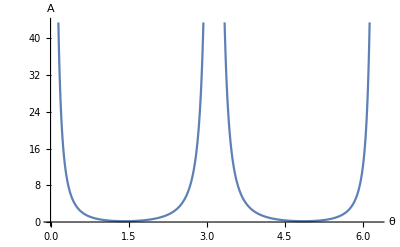

```mathematica
Plot[Aunit[traj, θ], {θ, 0, 2π},AxesLabel->{"θ","A"}]
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMC[ϕ_, ρ_]:=(-a0[ρ,ϕ])/(ρ(1- Cos[ϕ])(1+Cos[ϕ]))
```

Check This should be equal to Equation (1) for θ = π/2 and β=0:

```mathematica
FullSimplify[F[0,ϕ, π/2, ρ, τ] == AHMC[ϕ, ρ]]
```

True

Showing the change in the HMC integrated autocorrelation varying with acceptance rate,

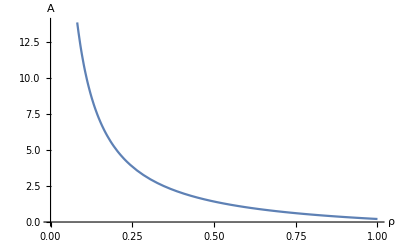

```mathematica
Plot[A[traj, π/2,ρ],{ρ, 0, 1},AxesLabel->{"ρ","A"}]
```

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMCunit[ϕ_] :=Cos[ϕ]^2/(1-Cos[ϕ]^2)
```

Check This should be equal to Equation (1) for θ=π/2, β=0 and ρ=1:

```mathematica
FullSimplify[AHMCunit[ϕ]==F[0, ϕ, π/2, 1, τ]]
```

True

## Inverse Laplace Transforms: Regular GHMC Autocorrelations

Inverting the autocorrelation functions gets very messy and so starting in reverse order now makes more sense, leaving the most complicated for last.

There is a sepcific method provided in the paper howeveτ, partial fraction decomposition is not well supported in Mathematica so it makes more sense to simply force the result for those that are not immediately obvious.

#### Important Note for Fixed Length Trajectories

The correlation function cannot be calculated by Mathematica. The code below is an artifact to deomonstrate this fact. The issue resides in the analytic form being that of a Dirac Comb so the result for the correlation functions is just a meaningless collection of Dirac Delta function infinities. See Appendix Section A2 of the referenced paper for the theory. As a result all the calculations are commented out to prevent a waste of computation.

## HMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
(*iFHMCunit = InverseLaplaceTransform[FHMCunit[β ,ϕ, τ],β,t] ;*)
(*CHMCunit[t_, ϕ_,τ_ ] := Evaluate[iFHMCunit]*)
```

Plotting shows the underdamped form for unit mass and averge trajector length τ,

```mathematica
(*Plot[CHMCunit[t, traj, rate]/CHMCunit[0,traj, rate], {t, 0, tf},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]*)
```

### HMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
(*iFHMC = InverseLaplaceTransform[FHMC[β ,ϕ, ρ, τ],β,t] ;
CHMC[t_, ϕ_, ρ_, τ_ ] := Evaluate[iFHMC]*)
```

Plotting for varying acceptance rate at t=0,

```mathematica
(*Plot[CHMC[0, traj, 1/ρ, traj], {ρ, 0, 1},AxesLabel->{"ρ","C(0)"}]*)
```

## GHMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
(*iFunit = InverseLaplaceTransform[Funit[β, ϕ, θ, τ],β,t];
Cunit[t_, ϕ_, θ_, τ_] := Evaluate[iFunit]*)
```

varying with mixing angle θ,

```mathematica
(*Plot3D[Cunit[t,traj,θ,1/traj]/Cunit[0,traj,θ,1/traj],{t,0,tf},{θ,0.15π,2 π-0.15π},PlotTheme->"Scientific",PlotRange->{0,1},AxesLabel->{"t","θ","C(t)"}]*)
```

### GHMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
(*iF = InverseLaplaceTransform[F[β, ϕ, θ, ρ, τ],β,t] ;
CF[t_, ϕ_, θ_,  ρ_, τ_] := Evaluate[iF]*)
```

varying with mixing angle θ and acceptance probability,

```mathematica
(*Plot3D[CF[t,traj,π/4,1/traj,ρ ]/CF[0,traj,π/4,1/traj,ρ ],{t,0,tf},{ρ ,0.6,1},PlotTheme->"Scientific",PlotRange->{0,1},AxesLabel->{"t","ρ","C(t)"}]*)
```

## Unit Test Results

```mathematica
Clear[bRng, thetaRng, rhoRng, phiRng, tauRng, tRng, nVars , ltSave, iacSave, iltSave, prec, zero]
```

Here are compiled a selectino of results to compare with the python implementation to verify correctness.

```mathematica
prec = 4; (* Number Precision *)
inf = 10^14; (* Inifinity threshold *)
zero = 10^-14;(* Zero threshold *)
```

#### Test Ranges

The test ranges are selected to hit key values as well as floating points that shouldn’t allow any simple cancellations,

```mathematica
bRng = { 0, 4.192};
thetaRng = {2π,0.12459};
rhoRng = { 1, 0.539};
phiRng = { 0.07, 4.79};
tauRng = {0.07, 2.7};
tRng = {0, 1, 5.79};
```

#### Save Names

The save locations for the data created to be compared to the python implementation,

```mathematica
ltSave = "__MMunittestLTfix_LT.csv"; (* laplace transform *)
iacSave="__MMunittestLTfix_iAC.csv"; (* integrated autocorrelation *)
iltSave="__MMunittestLTfix_iLT.csv";(* inverse laplace transform (autocorrelations) *)
```

## Laplace Transforms

```mathematica
Clear[ltDataset, nVars];
```

```mathematica
nVars = 5; (*Number of Function Variables: To create Table*)
ltDataset = Join[{{"beta","phi", "theta", "p_acc","tau", "F[beta, phi, theta, p_acc, 1/tau]"}},(*Title Line*)
Table[{β,ϕ, θ,ρ,τ, F[β,ϕ, θ,ρ, 1/τ] },(*Columns in Table*)
{β, bRng},{ϕ, phiRng}, {θ, thetaRng}, {ρ,rhoRng}, {τ, tauRng} ](*Iterate ranges*)
/. x_/;NumericQ[x] :>Re[ComplexExpand[x]] (* Remove zero complex parts *)
/.x_/; Abs[Simplify[x]]> inf :> "NaN"(* replace floating point infinities *)
/.x_/; Abs[x]< zero :> 0(* replace floating point zeros *)
//N[#,prec]& (* Force number precision *)
//Flatten[#,nVars-1]&] // Quiet;
ltDataset//Grid[#,Frame->All]&  (*Flatten List. Create Grid. Silent Errs.*)
```

beta | phi | theta | p_acc | tau | F[beta, phi, theta, p_acc, 1/tau]
0 | 0.07 | 6.283 | 1. | 0.07 | NaN
0 | 0.07 | 6.283 | 1. | 2.7 | NaN
0 | 0.07 | 6.283 | 0.539 | 0.07 | 5.93752×10^12
0 | 0.07 | 6.283 | 0.539 | 2.7 | 5.93752×10^12
0 | 0.07 | 0.12459 | 1. | 0.07 | 64.5477
0 | 0.07 | 0.12459 | 1. | 2.7 | 64.5477
0 | 0.07 | 0.12459 | 0.539 | 0.07 | 239.382
0 | 0.07 | 0.12459 | 0.539 | 2.7 | 239.382
0 | 4.79 | 6.283 | 1. | 0.07 | NaN
0 | 4.79 | 6.283 | 1. | 2.7 | NaN
0 | 4.79 | 6.283 | 0.539 | 0.07 | NaN
0 | 4.79 | 6.283 | 0.539 | 2.7 | NaN
0 | 4.79 | 0.12459 | 1. | 0.07 | 63.7563
0 | 4.79 | 0.12459 | 1. | 2.7 | 63.7563
0 | 4.79 | 0.12459 | 0.539 | 0.07 | 64.6168
0 | 4.79 | 0.12459 | 0.539 | 2.7 | 64.6168
4.192 | 0.07 | 6.283 | 1. | 0.07 | 0
4.192 | 0.07 | 6.283 | 1. | 2.7 | 0.266005
4.192 | 0.07 | 6.283 | 0.539 | 0.07 | 0
4.192 | 0.07 | 6.283 | 0.539 | 2.7 | 0.267446
4.192 | 0.07 | 0.12459 | 1. | 0.07 | 0
4.192 | 0.07 | 0.12459 | 1. | 2.7 | 0.266014
4.192 | 0.07 | 0.12459 | 0.539 | 0.07 | 0
4.192 | 0.07 | 0.12459 | 0.539 | 2.7 | 0.267448
4.192 | 4.79 | 6.283 | 1. | 0.07 | 0
4.192 | 4.79 | 6.283 | 1. | 2.7 | 0.0474848
4.192 | 4.79 | 6.283 | 0.539 | 0.07 | 0
4.192 | 4.79 | 6.283 | 0.539 | 2.7 | 0.126693
4.192 | 4.79 | 0.12459 | 1. | 0.07 | 0
4.192 | 4.79 | 0.12459 | 1. | 2.7 | 0.0467326
4.192 | 4.79 | 0.12459 | 0.539 | 0.07 | 0
4.192 | 4.79 | 0.12459 | 0.539 | 2.7 | 0.126384

## Integrated Autocorrelation Functions

```mathematica
Clear[iacDataset, nVars];
```

```mathematica
nVars = 4; 
iacDataset = Join[{{"phi", "theta", "p_acc", "tau","A[phi, theta, p_acc]", "F[0, phi, theta, p_acc, 1/tau] "}},(*Title Line*)
Table[{ϕ, θ, ρ,τ, A[ϕ, θ, ρ],F[0,ϕ, θ,ρ, 1/τ] },(*Columns in Table*)
{ϕ, phiRng}, {θ, thetaRng}, {ρ,rhoRng},{τ, tauRng}](*Iterate ranges*)
/. x_/;NumericQ[x] :>Re[ComplexExpand[x]] (* Remove zero complex parts *)
/.x_/; Abs[Simplify[x]]> inf :> "NaN"(* replace floating point infinities *)
//N[#,prec]& (* Force number precision *)
//Flatten[#,nVars-1]&]// Quiet;(*Flatten List. Silent Errs.*)
iacDataset//Grid[#,Frame->All]&  (*Create Grid.*)
```

phi | theta | p_acc | tau | A[phi, theta, p_acc] | F[0, phi, theta, p_acc, 1/tau] 
0.07 | 6.283 | 1. | 0.07 | NaN | NaN
0.07 | 6.283 | 1. | 2.7 | NaN | NaN
0.07 | 6.283 | 0.539 | 0.07 | NaN | 5.93752×10^12
0.07 | 6.283 | 0.539 | 2.7 | NaN | 5.93752×10^12
0.07 | 0.12459 | 1. | 0.07 | 64.5477 | 64.5477
0.07 | 0.12459 | 1. | 2.7 | 64.5477 | 64.5477
0.07 | 0.12459 | 0.539 | 0.07 | 239.382 | 239.382
0.07 | 0.12459 | 0.539 | 2.7 | 239.382 | 239.382
4.79 | 6.283 | 1. | 0.07 | NaN | NaN
4.79 | 6.283 | 1. | 2.7 | NaN | NaN
4.79 | 6.283 | 0.539 | 0.07 | NaN | NaN
4.79 | 6.283 | 0.539 | 2.7 | NaN | NaN
4.79 | 0.12459 | 1. | 0.07 | 63.7563 | 63.7563
4.79 | 0.12459 | 1. | 2.7 | 63.7563 | 63.7563
4.79 | 0.12459 | 0.539 | 0.07 | 64.6168 | 64.6168
4.79 | 0.12459 | 0.539 | 2.7 | 64.6168 | 64.6168

## Inverse Laplace Transforms

```mathematica
Clear[iltDataset, nVars];
```

Instead of wasting time inverting the entire function, values are set as constants beforehand,

Note: As above - this transform cannot be calculated

```mathematica
(*nVars = 5; (*Number of Function Variables: To create Table*)
iltDataset = Join[{{"t","tau","phi","theta","p_acc", "invL[F[beta, phi, theta, p_acc, 1/tau]](t)"}},(*Title Line*)
Table[{t,τ , ϕ, θ,ρ,InverseLaplaceTransform[F[β, ϕ, θ,  ρ, 1/τ],β,t]},(*Columns in Table*)
{t, tRng},{τ, tauRng},{ϕ, phiRng},{θ, thetaRng}, {ρ,rhoRng} ] (*Iterate ranges*)
/. x_/;NumericQ[x] :>Re[ComplexExpand[x]] (* Remove zero complex parts *)
/.x_/; Abs[Simplify[x]]> inf :> "NaN"(* replace floating point infinities *)
/.x_/; Abs[x]< zero :> 0(* replace floating point zeros *)
//N[#,prec]& (* Force number precision *)
//Flatten[#,nVars-1]&]//Quiet;(*Flatten List. Silent Errs.*)
iltDataset//Grid[#,Frame->All]&  (*Create Grid.*)*)
```

## Export Data to CSV

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export[ltSave,ltDataset,"CSV",CharacterEncoding->"UTF8"]
Export[iacSave,iacDataset,"CSV",CharacterEncoding->"UTF8"]
(*Export[iltSave,iltDataset,"CSV",CharacterEncoding->"UTF8"]*)
```

__MMunittestLTfix_LT.csv

__MMunittestLTfix_iAC.csv